```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=r>=0&&Q>=0&&M>0&&α>0;
SetDirectory[NotebookDirectory[]];
tickfunc[xmin_,xmax_]:=Table[{x,NumberForm[x,20]},{x,xmin,xmax,(xmax-xmin)/4}];
ℱRNac=(1−(2M)/r+Q^2/r^2)(1−ξ((2M)/r−Q^2/r^2) (1−(2M)/r+Q^2/r^2));
ℱRNac1=(1−(2M)/r+Q^2/r^2);
ℱRNac2=(1−ξ((2M)/r−Q^2/r^2) (1−(2M)/r+Q^2/r^2));
ℱ[M_]:=(1−(2M)/r)(1−ξ((2M)/r) (1−(2M)/r));
ℱ1[M_]:=(1−(2M)/r);
ℱ2[M_]:=(1−ξ((2M)/r) (1−(2M)/r));
MRN=M;
MDEC=M(1-1/((1+((2 M r)/Q^2)^3)^(1/3)));
MABG=M (r^3/((r^2+Q^2)^(3/2))-(Q^2 r^3)/(2M(r^2+Q^2)^2));
Mtanh=M (1-Tanh[Q^2/(2 M r)]);
Mexp=M Exp[-Q^2/(2M r)];
ξmaxw=ξ/.Solve[ℱRNac==0,ξ]//FullSimplify;
ξmod1=ξ/.Solve[ℱ[Mmod1]==0,ξ]//FullSimplify;
ξmod2=ξ/.Solve[ℱ[Mmod2]==0,ξ]//FullSimplify;
ξtanh=ξ/.Solve[ℱ[Mtanh]==0,ξ]//FullSimplify;
ξexp=ξ/.Solve[ℱ[Mexp]==0,ξ]//FullSimplify;
```

```mathematica
Mmod3=((MDEC α) +(MABG(1-α)))//FullSimplify
ℱ1[Mmod3]
Series[%,{r,∞,6}]//Simplify
```

M (-(Q^2 r^3)/(2 M (Q^2+r^2)^2)+r^3/((Q^2+r^2)^(3/2))) (1-α)+M (1-1/((1+(8 M^3 r^3)/Q^6)^(1/3))) α

1-(2 (M (-(Q^2 r^3)/(2 M (Q^2+r^2)^2)+r^3/((Q^2+r^2)^(3/2))) (1-α)+M (1-1/((1+(8 M^3 r^3)/Q^6)^(1/3))) α))/r

1-(2 M)/r+Q^2/r^2-(3 (M Q^2 (-1+α)))/r^3+(2 Q^4 (-1+α))/r^4+(15/4 M Q^4 (-1+α)-(Q^8 α)/(24 M^3))/r^5-(3 (Q^6 (-1+α)))/r^6+O[1/r]^7

```mathematica
ℱ[Mmod3]==0
```

(1-(2 (M+(Q^2 r^3 (-1+α))/(2 (r^2-Q^2 (-1+α))^2)-(M Q^2 α)/((8 M^3 r^3+Q^6 α^3)^(1/3))))/r) (1-(2 (M+(Q^2 r^3 (-1+α))/(2 (r^2-Q^2 (-1+α))^2)-(M Q^2 α)/((8 M^3 r^3+Q^6 α^3)^(1/3))) (1-(2 (M+(Q^2 r^3 (-1+α))/(2 (r^2-Q^2 (-1+α))^2)-(M Q^2 α)/((8 M^3 r^3+Q^6 α^3)^(1/3))))/r) ξ)/r)==0

```mathematica
ℱ[Mmod3]/.{M->1,Q->0.8,ξ->5}//FullSimplify
```

$Aborted

```mathematica
α/.NSolve[(ℱ[Mmod3]/.{M->1,Q->0.8,ξ->5})==0,α][[1]]
```

$Aborted

{0.999993,0.999926}

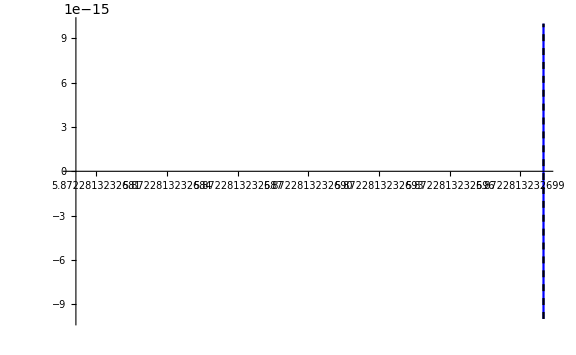

```mathematica
ini={1.866024,5.872281323268,0};
fin={1.866041,5.87228132327,10};
αX={.99999346463,.9999255}
parameter={M->1,Q->0.5,ξ->4.5,α->αX[[1]]};
Plot[{ℱ[Mmod3]/.parameter,ℱ[MDEC]/.parameter,ℱRNac/.parameter},{r,ini[[2]],fin[[2]]},PlotRange->{-10^-14,10^-14},PlotStyle->{Blue,Red,{Black,Dashed}},ImageSize->Large]
```

```mathematica
Mwaaa=M(2/(1+Exp[Q^2/(β M r)]))^β
MABG2=M((1/(1+γ(Q^2/(M r))^α))^(3/α)-Q^2/(2 M r)(1/(1+γ(Q^2/(M r))^α))^(4/α))//FullSimplify
```

2^β (1/(1+ⅇ^(Q^2/(M r β))))^β M

M (1/(1+Q^(2 α) (M r)^-α γ))^(3/α)-(Q^2 (1/(1+Q^(2 α) (M r)^-α γ))^(4/α))/(2 r)

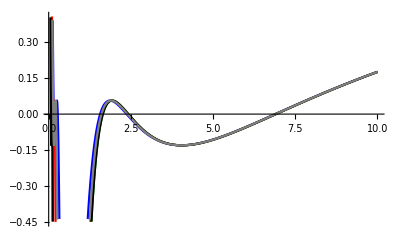

```mathematica
parameter={M->1,Q->0.8,ξ->5};
ini=.001;
fin=10;
β1=Plot[ℱ[Mwaaa]/.parameter/.β->0.5,{r,ini,fin},PlotStyle->Blue];
β2=Plot[ℱ[Mwaaa]/.parameter/.β->2,{r,ini,fin},PlotStyle->Red];
β3=Plot[ℱ[Mwaaa]/.parameter/.β->100,{r,ini,fin},PlotStyle->Darker@Green];
βexp=Plot[ℱ[Mexp]/.parameter,{r,ini,fin},PlotStyle->Black];
βtanh=Plot[ℱ[Mtanh]/.parameter,{r,ini,fin},PlotStyle->Gray];
Show[β1,β2,β3,βexp,βtanh,PlotRange->Automatic]
```

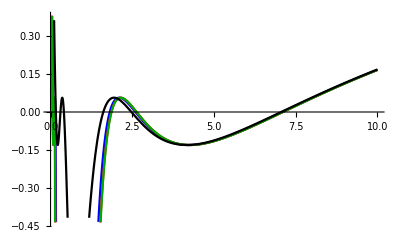

```mathematica
parameter={M->1,Q->0.5,ξ->5,γ->1};
ini=0;
fin=10;
α1=Plot[ℱ[MABG2]/.parameter/.α->2,{r,ini,fin},PlotStyle->Blue];
α2=Plot[ℱ[MABG2]/.parameter/.α->3,{r,ini,fin},PlotStyle->Red];
α3=Plot[ℱ[MABG2]/.parameter/.α->4,{r,ini,fin},PlotStyle->Darker@Green];
αABG=Plot[ℱ[Mmod2]/.parameter,{r,ini,fin},PlotStyle->Black];
Show[α1,α2,α3,αABG]
```

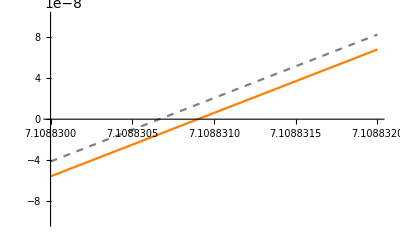

```mathematica
parameter={M->1,Q->0.5,ξ->5,α->2};
ini=7.10883;
fin=7.108832;
γ1=Plot[ℱ[MABG2]/.parameter/.γ->0.1,{r,ini,fin},PlotStyle->Blue,PlotRange->{-1,1.2}];
γ2=Plot[ℱ[MABG2]/.parameter/.γ->3,{r,ini,fin},PlotStyle->Red,PlotRange->{-1,1.2}];
γ3=Plot[ℱ[MABG2]/.parameter/.γ->5,{r,ini,fin},PlotStyle->Darker@Green,PlotRange->{-1,1.2}];
γABG=Plot[ℱ[Mmod2]/.parameter,{r,ini,fin},PlotStyle->Black,PlotRange->{-1,1.2}];
γMaxw=Plot[ℱRNac/.parameter,{r,ini,fin},PlotStyle->{Gray,Dashed},PlotRange->{-1,1.2}];
γDEC=Plot[ℱ[Mmod1]/.parameter,{r,ini,fin},PlotStyle->{Orange},PlotRange->{-1,1.2}];
Show[γ1,γ2,γ3,γABG,γDEC,γMaxw,PlotRange->{-.0000001,.0000001}]
```

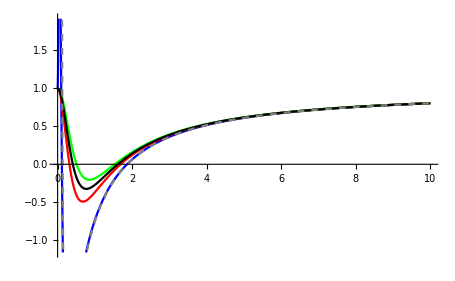

```mathematica
parameter={M->1,Q->0.5,ξ->5,α->2};
ini=0;
fin=10;
γ1=Plot[ℱ1[MABG2]/.parameter/.γ->0.1,{r,ini,fin},PlotStyle->Blue];
γ2=Plot[ℱ1[MABG2]/.parameter/.γ->3,{r,ini,fin},PlotStyle->Red];
γ3=Plot[ℱ1[MABG2]/.parameter/.γ->5,{r,ini,fin},PlotStyle->Green];
γABG=Plot[ℱ1[Mmod2]/.parameter,{r,ini,fin},PlotStyle->Black];
γMaxw=Plot[ℱRNac1/.parameter,{r,ini,fin},PlotStyle->{Gray,Dashed}];
Show[γ1,γ2,γ3,γABG,γMaxw]
```

### Plot horizontes según ξ

#### tanh

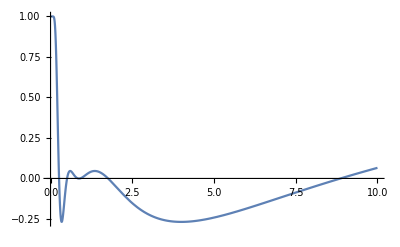

```mathematica
Plot[ℱ[Mtanh]/.{M->1,Q->1.055,ξ->6},{r,0,10},PlotRange->All]
```

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξtanh=ξ/.Solve[ℱ[Mtanh]==0,ξ]//FullSimplify;
tanhsolPlot=ParametricPlot[{ξtanh[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Thin,Blue}]
```

-Graphics-

#### mod2 (ABG - Perez)

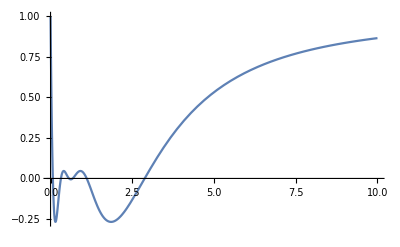

```mathematica
Plot[ℱ[Mmod2]/.{M->1,Q->0.875,ξ->6},{r,0,10}]
```

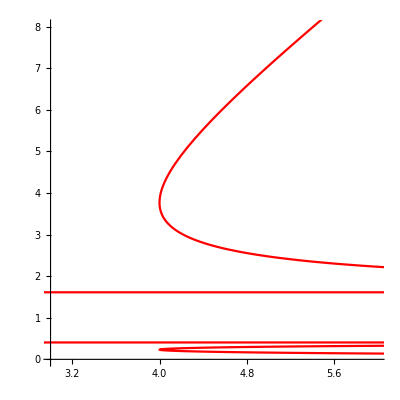

```mathematica
parameter={M->1,Q->0.5,ξ->5};
ξmod2=ξ/.Solve[ℱ[Mmod2]==0,ξ]//FullSimplify;
mod2solPlot=ParametricPlot[{ξmod2[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Red}]
```

#### mod1 (DEC)

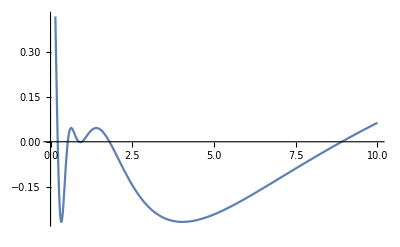

```mathematica
Plot[ℱ[Mmod1]/.{M->1,Q->1.025,ξ->6},{r,0,10}]
```

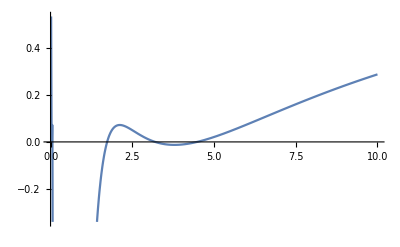

```mathematica
Plot[ℱ[rmod1]/.{M->1,Q->0.5,ξ->4.1},{r,0,10}]
```

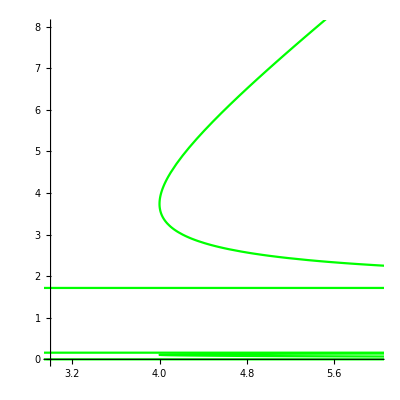

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξmod1=ξ/.Solve[ℱ[Mmod1]==0,ξ]//FullSimplify;
mod1solPlot=ParametricPlot[{ξmod1[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Green}]
```

#### exp

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξexp=ξ/.Solve[ℱ[Mexp]==0,ξ]//FullSimplify;
expsolPlot=ParametricPlot[{ξexp[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Orange}]
```

-Graphics-

#### maxwell

```mathematica
Plot[ℱ[Mmod1]/.{M->1,Q->1.025,ξ->6},{r,0,10}]
```

```mathematica
Ξ=√(ξ^2-4ξ);
Xξ=2 M^2 ξ^2-4 M^2 ξ-2ξ Q^2;
Yξ=(8 M^3 ξ^3-8M ξ(4 M^2 ξ+ξ Q^2)+32M ξ Q^2)/(4 M √(ξ^2-4ξ));
rc=M-√((M-Q) (M+Q));
rh=M+√((M-Q) (M+Q));
ra1=(M ξ)/2-1/2 M Ξ - 1/2 √(Xξ-Yξ);
ra2=(M ξ)/2-1/2 M Ξ + 1/2 √(Xξ-Yξ);
ra3=(M ξ)/2+1/2 M Ξ - 1/2 √(Xξ+Yξ);
ra4=(M ξ)/2+1/2 M Ξ + 1/2 √(Xξ+Yξ);
ra1Plot=Plot[ra1/.{M->1,Q->1/2},{ξ,3.5,8}];
ra2Plot=Plot[ra2/.{M->1,Q->1/2},{ξ,3.5,8}];
ra3Plot=Plot[ra3/.{M->1,Q->1/2},{ξ,3.5,8}];
ra4Plot=Plot[ra4/.{M->1,Q->1/2},{ξ,3.5,8}];
rcPlot=Plot[rc/.{M->1,Q->1/2},{ξ,3.5,8}];
rhPlot=Plot[rh/.{M->1,Q->1/2},{ξ,3.5,8}];
plotMaxwell=Show[ra1Plot,ra2Plot,ra3Plot,ra4Plot,rcPlot,rhPlot,PlotRange->All];
```

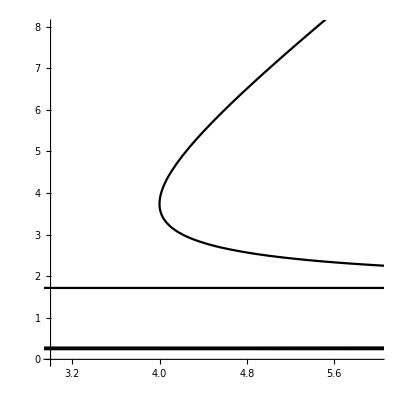

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξmaxw=ξ/.Solve[ℱRNac==0,ξ]//FullSimplify;
maxwsolPlot=ParametricPlot[{ξmaxw[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Black}]
```

#### todo

Negro=Maxwell, Rojo=DEC, Verde=ABG, Azul=Tanh, Naranjo=exp

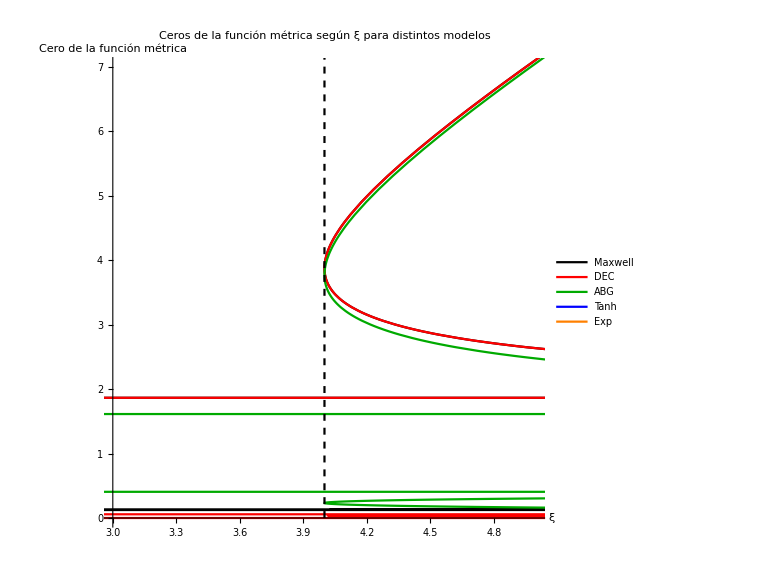
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξmod1[[1]]/.parameter,r},{ξmod2[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,10},PlotRange->{{3,5},{0,7}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_General.png",%,"PNG"];
```

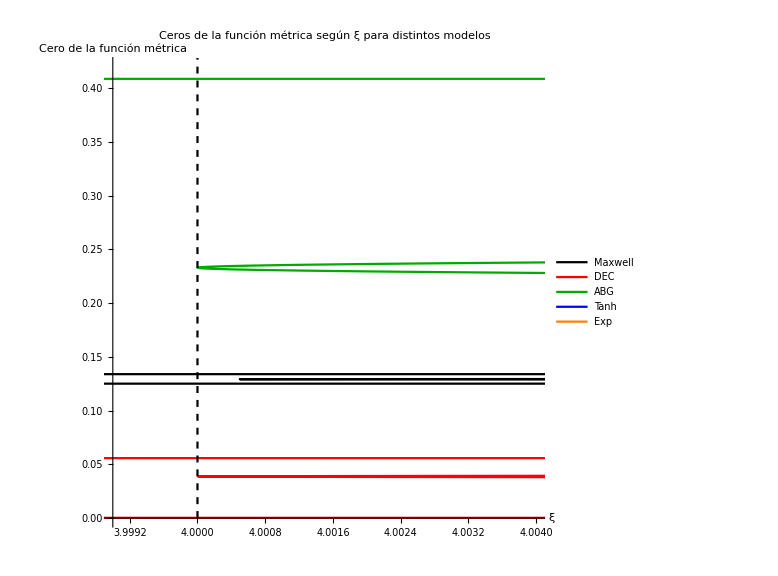
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξmod1[[1]]/.parameter,r},{ξmod2[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,10},PlotRange->{{3.999,4.004},{0,0.42}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->1000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom1.png",%,"PNG"];
```

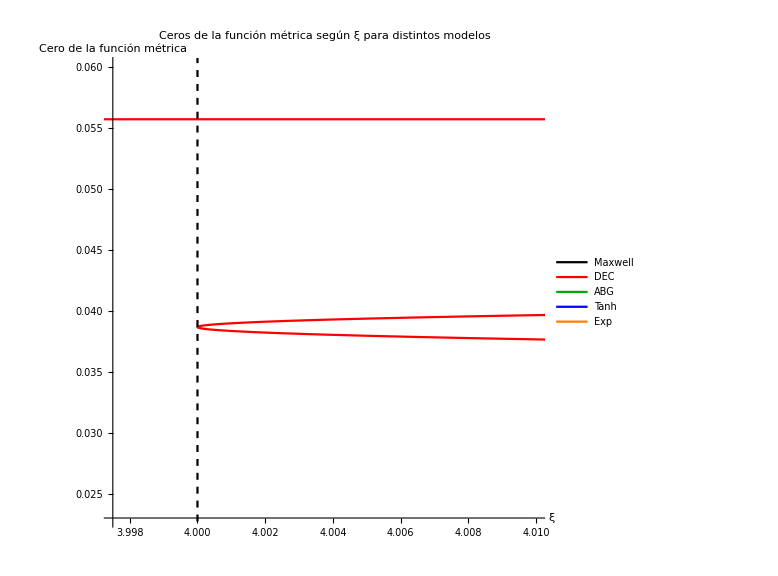
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξmod1[[1]]/.parameter,r},{ξmod2[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,0.1},PlotRange->{{3.9975,4.01},{0.023,0.06}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->1000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom2.png",%,"PNG"];
```

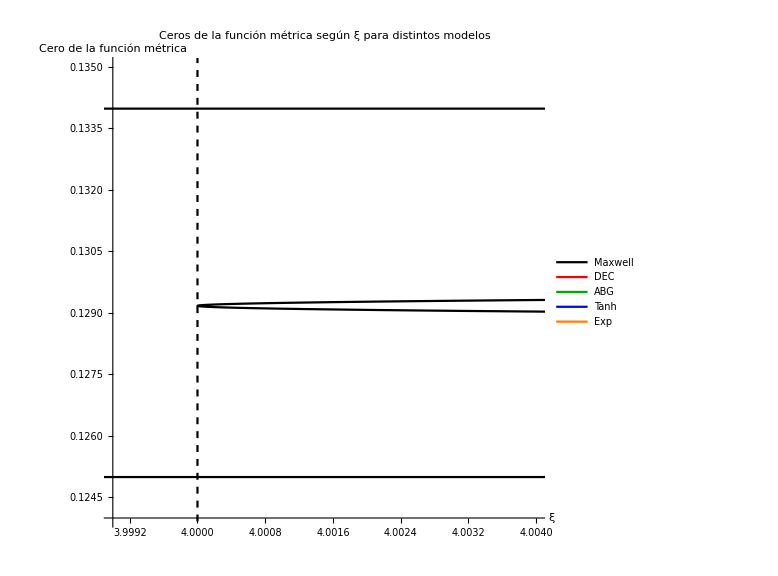
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξmod1[[1]]/.parameter,r},{ξmod2[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,0.5},PlotRange->{{3.999,4.004},{.124,.135}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->3000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom3.png",%,"PNG"];
```

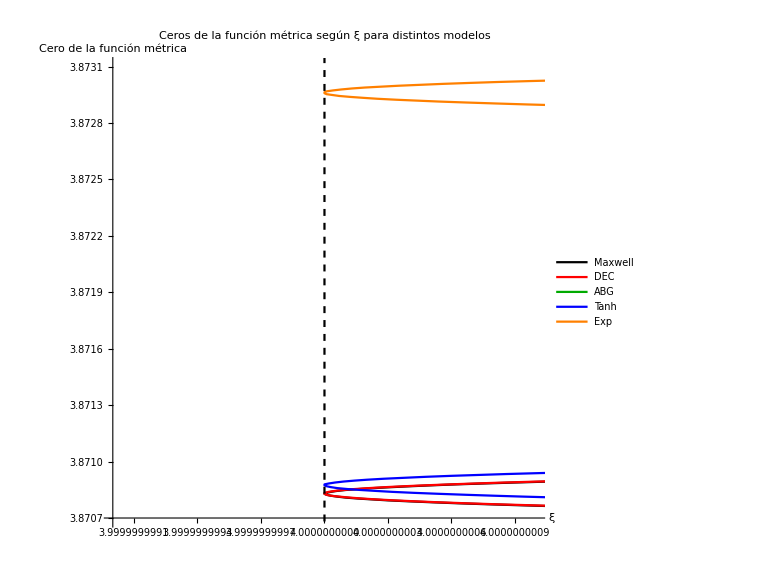
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξmod1[[1]]/.parameter,r},{ξmod2[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,3.85,3.9},PlotRange->{{3.999999999,4.000000001},{3.8707,3.8731}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->5000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},Ticks->{tickfunc,Automatic},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom4.png",%,"PNG"];
```

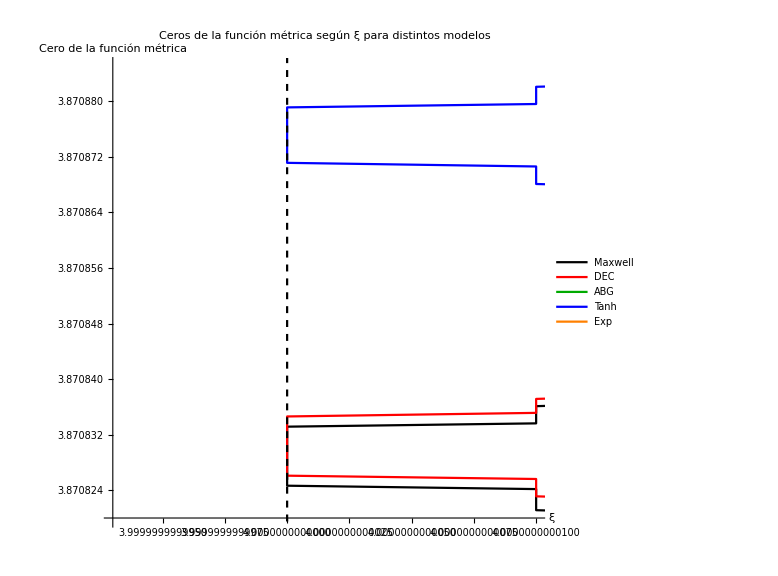
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξmod1[[1]]/.parameter,r},{ξmod2[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,3.87,3.875},PlotRange->{{3.999999999993,4.00000000001},{3.87082,3.870885}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->5000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},Ticks->{tickfunc,Automatic},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom5.png",%,"PNG"];
```

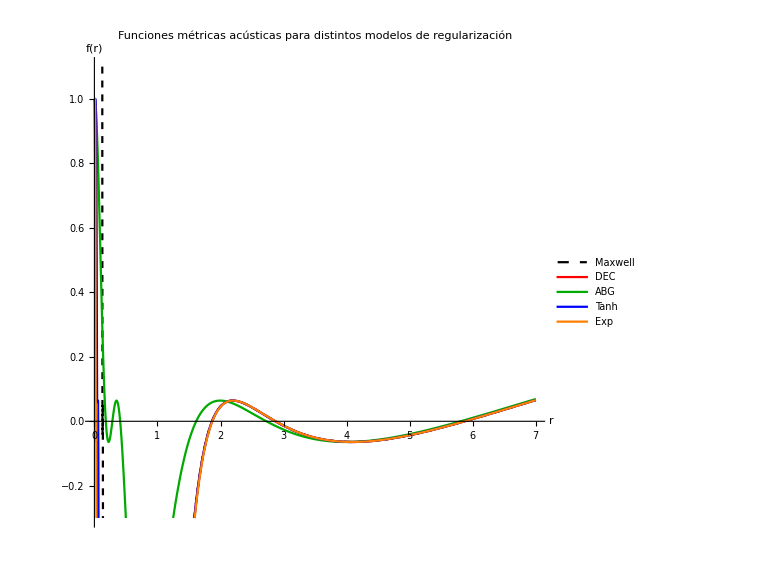
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,.001,7},PlotRange->{-.3,1.1},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_General.png",%,"PNG"];
```

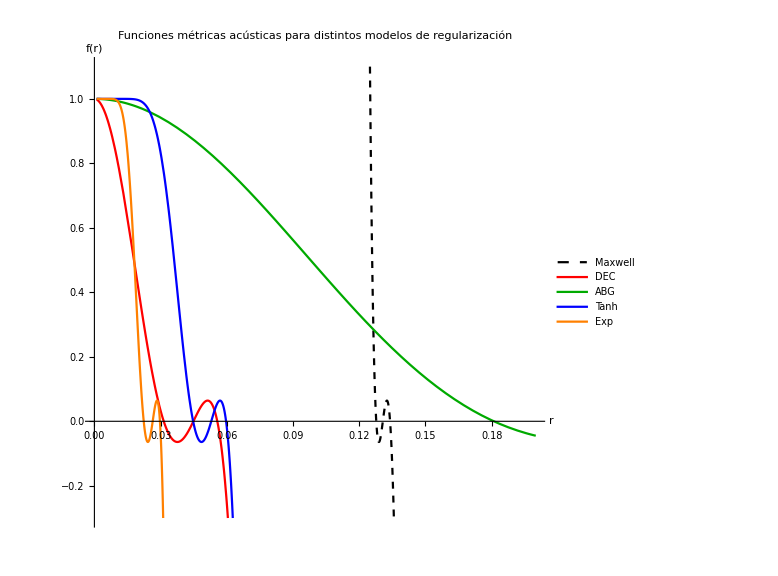
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,.001,.2},PlotRange->{-.3,1.1},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom1.png",%,"PNG"];
```

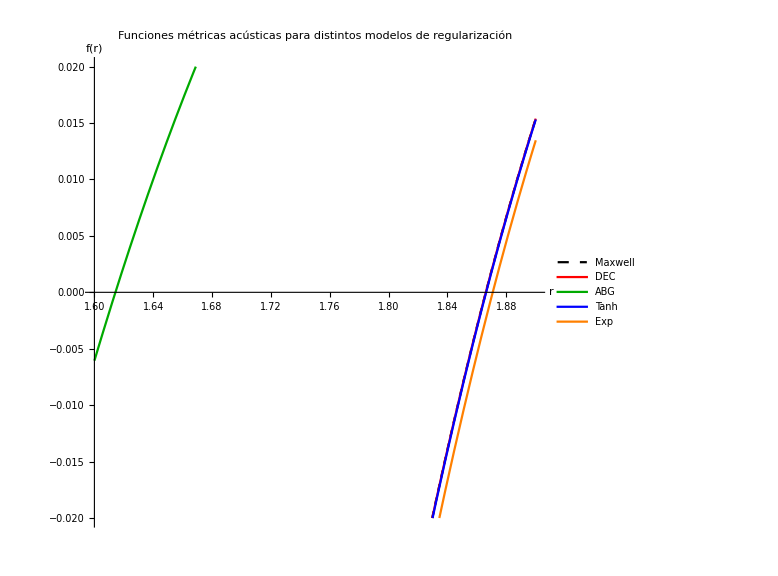
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,1.6,1.9},PlotRange->{-.02,.02},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom2.png",%,"PNG"];
```

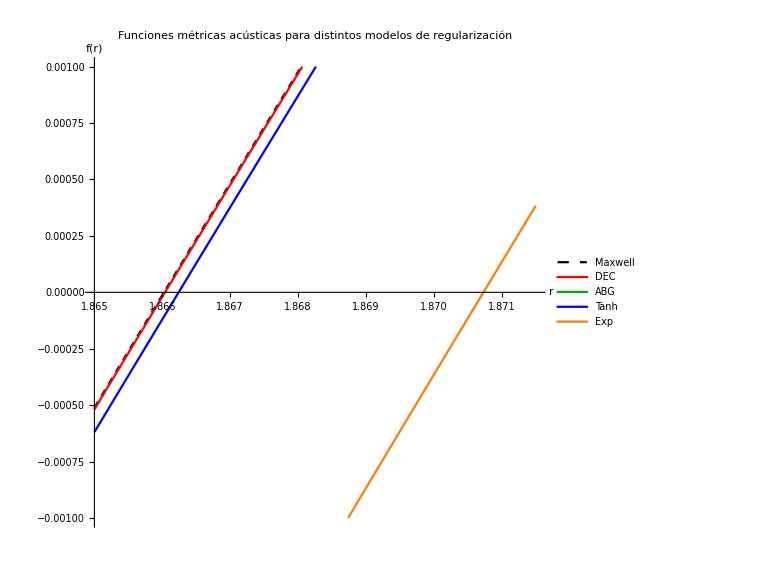
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,1.865,1.8715},PlotRange->{-.001,.001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom3.png",%,"PNG"];
```

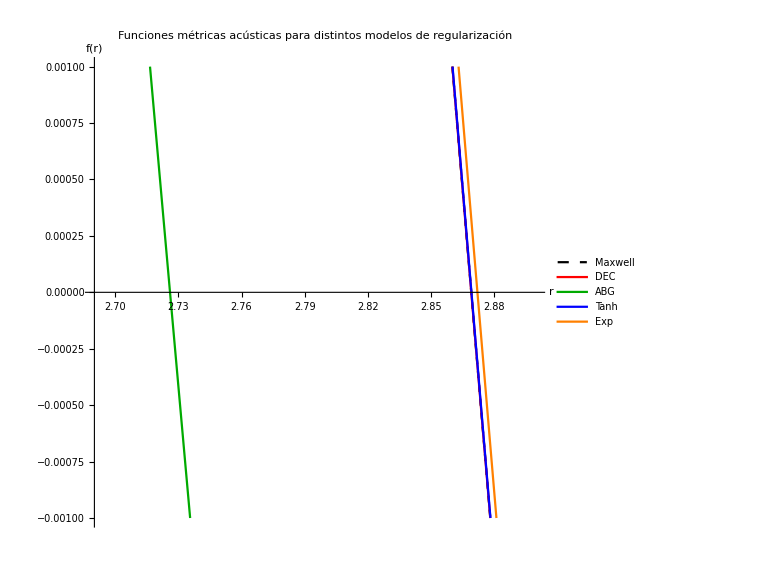
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,2.69,2.9},PlotRange->{-.001,.001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom4.png",%,"PNG"];
```

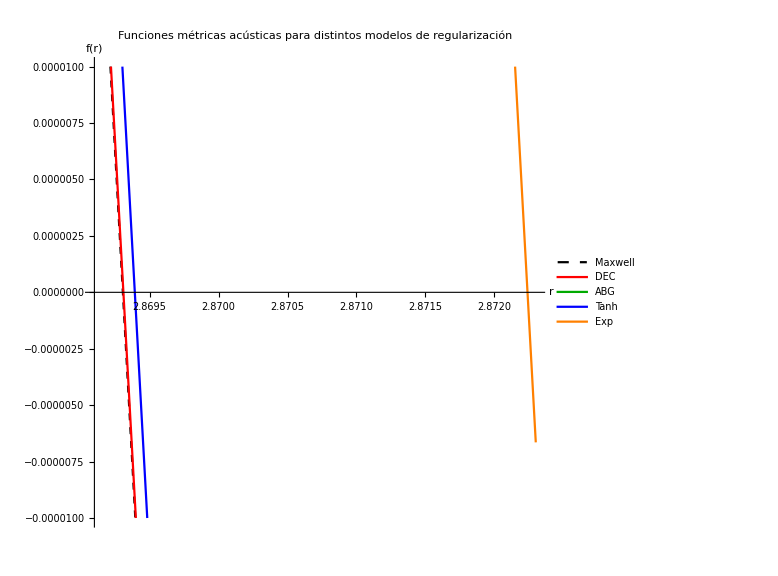
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,2.8691,2.8723},PlotRange->{-.00001,.00001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom5.png",%,"PNG"];
```

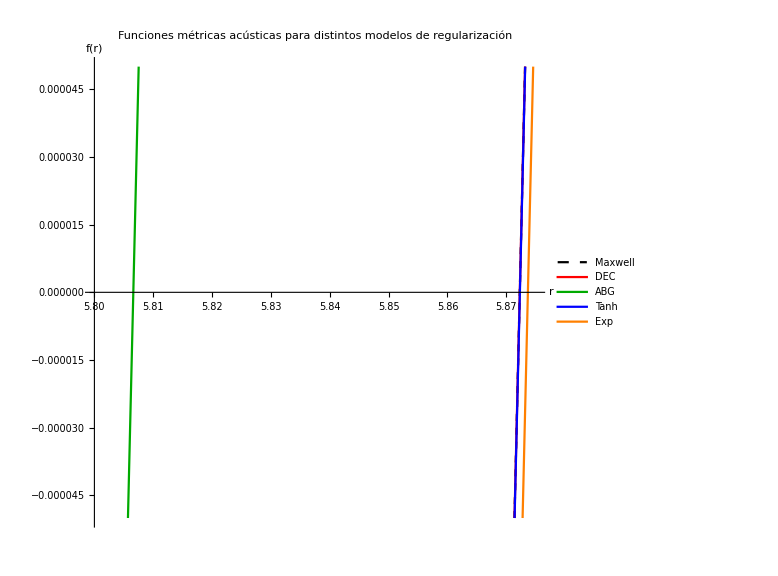
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,5.8,5.875},PlotRange->{-.00005,.00005},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom6.png",%,"PNG"];
```

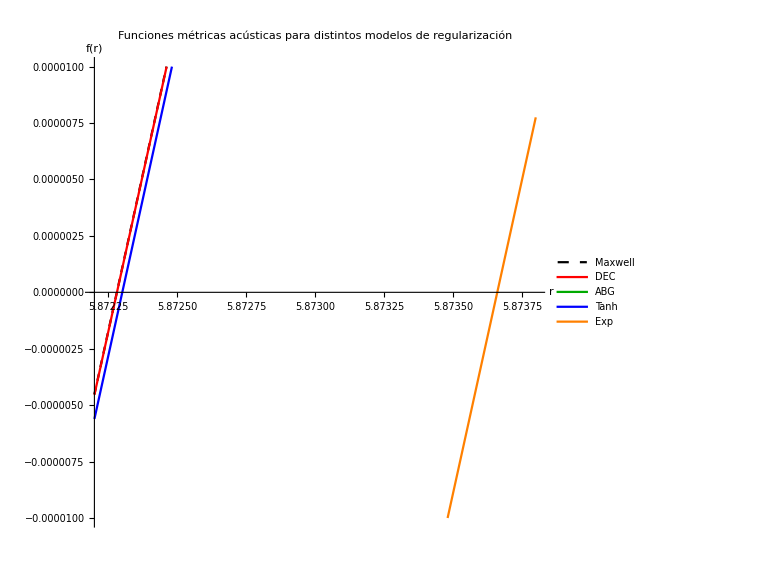
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,5.8722,5.8738},PlotRange->{-.00001,.00001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom7.png",%,"PNG"];
```

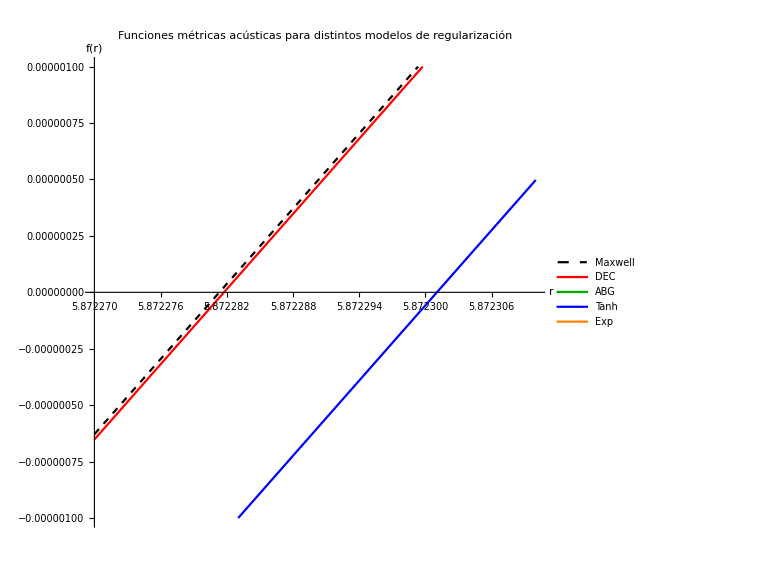
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[Mmod1]/.parameter,ℱ[Mmod2]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,5.87227,5.87231},PlotRange->{-.000001,.000001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom8.png",%,"PNG"];
```

### Tabla

```mathematica
Parametros={M->1,Q->0.7,ξ->4.5};
a[1,1]="Modelo";
a[1,2]="Rc";
a[1,3]="Rh";
a[2,1]="Maxwell";
a[3,1]="DEC";
a[4,1]="ABG";
a[5,1]="Tanh";
a[6,1]="Exp";
a[2,2]=r/.NSolve[ℱRNac1/.Parametros,r,PositiveReals];
a[3,2]=r/.NSolve[ℱ1[Mmod1]/.Parametros,r,PositiveReals];
a[4,2]=r/.NSolve[ℱ1[Mmod2]/.Parametros,r,PositiveReals];
a[5,2]=r/.NSolve[ℱ1[Mtanh]/.Parametros,r,PositiveReals];
a[6,2]=r/.NSolve[ℱ1[Mexp]/.Parametros,r,PositiveReals];
a[2,3]=r/.NSolve[ℱRNac2/.Parametros,r,PositiveReals];
a[3,3]=r/.NSolve[ℱ2[Mmod1]/.Parametros,r,PositiveReals];
a[4,3]=r/.NSolve[ℱ2[Mmod2]/.Parametros,r,PositiveReals];
a[5,3]=r/.NSolve[ℱ2[Mtanh]/.Parametros,r,PositiveReals];
a[6,3]=r/.NSolve[ℱ2[Mexp]/.Parametros,r,PositiveReals];
TableForm[Flatten@Array[a,{6,3}][[#]]&/@Range[Length@Array[a,{6,3}]]]
```

Modelo | Rc | Rh |  |  |  | 
Maxwell | 0.285857 | 1.71414 | 0.255915 | 0.269147 | 2.73085 | 5.74408
DEC | 0.161787 | 1.71448 | 0.087015 | 0.126653 | 2.73093 | 5.74409
ABG | 0.191006 | 1.09275 | 0.0577513 | 0.119355 | 1.49195 | 2.29087
Tanh | 0.151463 | 1.71645 | 0.103219 | 0.128101 | 2.73165 | 5.74425
Exp | 0.0744508 | 1.73688 | 0.0514911 | 0.0635654 | 2.74373 | 5.74971

Jueves : enviar graficos con caption
Viernes : comportamiento por familia

```mathematica
2da y 3ra condición graficar
```